```mathematica
Taller 10.1
```

```mathematica
Clear[f]
Clear[g]
```

-10-3 x+x Cos[3+6 x]+Log[1+x^2]

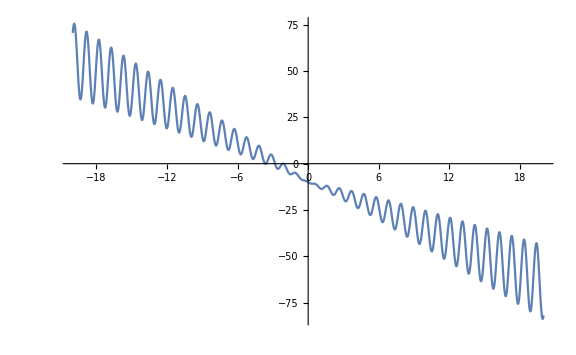

```mathematica
f[x_] := Log[x^2+1]+x*Cos[6x+3]-3x-10
f[x]
Plot[f[x],{x,-20,20},PlotRange->Automatic,ImageSize->Large]
```

```mathematica
BISECCION
```

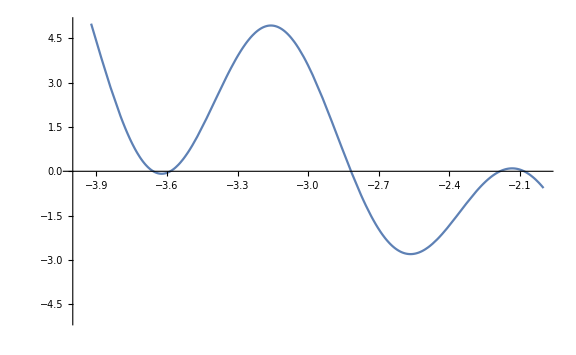

```mathematica
Plot[f[x],{x,-4,-2},PlotRange->{-5,5},ImageSize->Large]
```

```mathematica
Punto Fijo
```

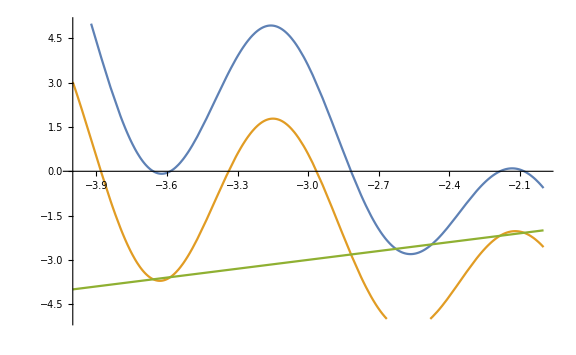

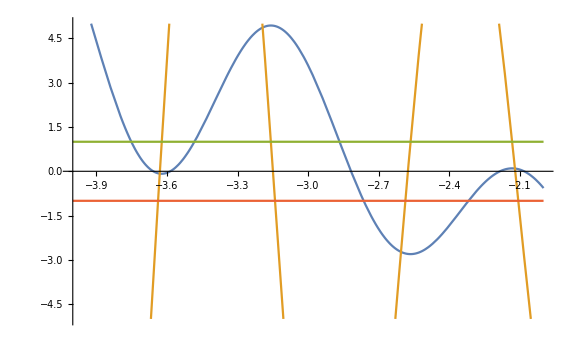

```mathematica
g[x_] := Log[x^2+1]+x*Cos[6x+3]-2x-10
Plot[{f[x],g[x],x},{x,-4,-2},PlotRange->{-5,5},ImageSize->Large]
Plot[{f[x],g'[x],1,-1},{x,-4,-2},PlotRange->{-5,5},ImageSize->Large]
```

```mathematica
Newton / Secante
```

-3+(2 x)/(1+x^2)+Cos[3+6 x]-6 x Sin[3+6 x]

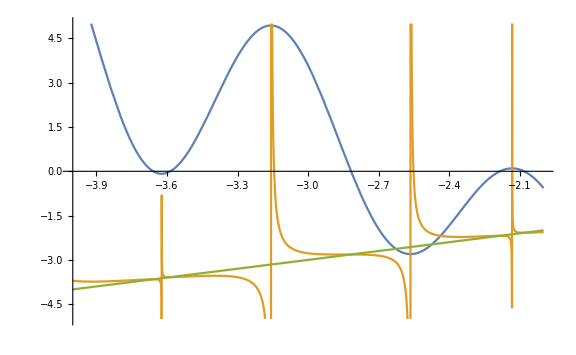

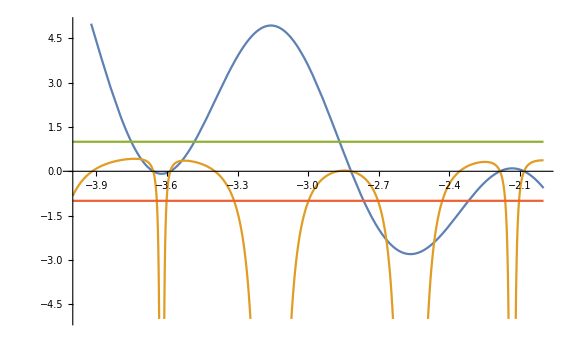

```mathematica
f'[x]
g[x_] :=x-f[x]/f'[x]
Plot[{f[x],g[x],x},{x,-4,-2},PlotRange->{-5,5},ImageSize->Large]
Plot[{f[x],g'[x],1,-1},{x,-4,-2},PlotRange->{-5,5},ImageSize->Large]
```

```mathematica
Raices multiples
```

-(4 x^2)/((1+x^2)^2)+2/(1+x^2)-36 x Cos[3+6 x]-12 Sin[3+6 x]

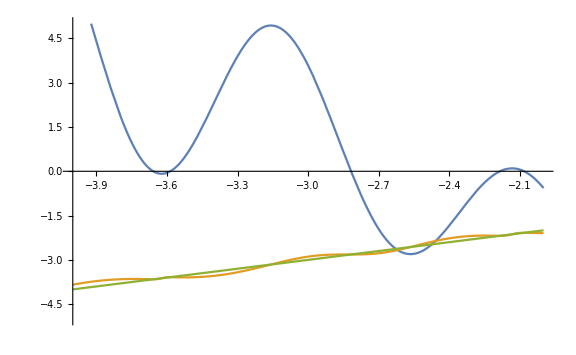

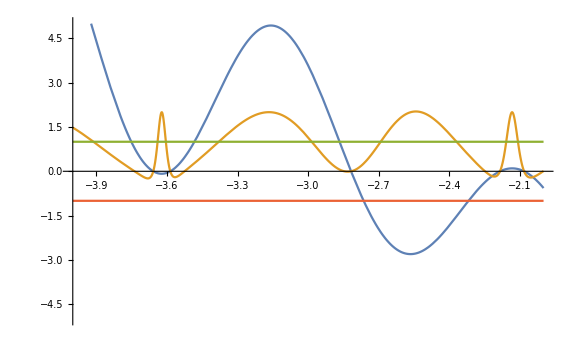

```mathematica
f''[x]
g[x_] := x-(f[x]*f'[x])/(f'[x]^2-f[x]*f''[x])
Plot[{f[x],g[x],x},{x,-4,-2},PlotRange->{-5,5},ImageSize->Large]
Plot[{f[x], g'[x], 1, -1},{x,-4,-2},PlotRange->{-5,5},ImageSize->Large]
```